## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_,κ_}]:=Module[{gridLabel,gridData},
gridLabel={"k","(X^k)","f(X^k)","||w^k||","κ"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
gridData[[All,4]]=SetAccuracy[norms,4];
(*в 4-м столбце-значение нормы невязки*)
gridData[[All,5]]=SetAccuracy[κ,4];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,setX_,setY_,{points_,fValues_}]:=Module[{},
ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
```

## Метод Ньютона:

```mathematica
Antigrad[point_, func_] := -Grad[func[{x, y}], {x, y}] /. {x->point[[1]],y->point[[2]]};
Hesse[ func_] := D[func[{x,y}],{{x,y},2}] ;
CalcHesse[MHesse_,{xp_,yp_}]:=MHesse/.{x -> xp, y -> yp};
MakePositive[Hesse_,k_]:=Module[{H = Hesse,n = Length@Hesse},
If[PositiveDefiniteMatrixQ[Hesse],
Return[H],
H = MakePositive[H+k*IdentityMatrix[n],k];
];
Return[H]
];
```

```mathematica
Algorithm[{x0_, y0_},func_,ϵ_,split_,w_,ν_] :=Module [
{
points = {{x0, y0}},
funcpoints = {},
ω = {},
norms = {},
H = Hesse[func],
CalcH,
InvH,
CalcInvH,
Positive,
κ={1}
},
Positive = PositiveDefiniteMatrixQ[H];
InvH = Inverse[H];
funcpoints ={ func[Last@points] };
ω = {Antigrad[Last@points, func]};
norms = {Norm[Last@ω]};
While[Last@norms ≥ ϵ,
If[Not@Positive,
CalcH = MakePositive[CalcHesse[H,Last@points],10];
CalcInvH = Inverse[CalcH],
CalcInvH = CalcHesse[InvH,Last@points];
];
AppendTo[points, Last@points +Last@κ* CalcInvH .Last@ω//N];
AppendTo[funcpoints, func[Last@points]];
If[split,
If[funcpoints[[-1]]-funcpoints[[-2]]≥ -w*Last@κ*(Last@ω.(CalcInvH.Last@ω)),
AppendTo[κ,Last@κ],
AppendTo[κ,Last@κ*ν];
];
];

AppendTo[ω, Antigrad[Last@points, func] ];
AppendTo[norms, Norm[Last@ω]];

] ;
{points, funcpoints, norms,κ}
];
```

## Функции:

```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
g[{x_,y_}]:=8 x^2+5 y^2-4x y + 8 √5(x+2y)+64;
rosenbrok[{x_,y_}]:=(1-x)^2+200(y-x^2)^2;
```

## Рабочая зона:

### Первый пример:

```mathematica
func =g;(*x0 = {√5,0}, x1 = {0 , 2 √5}*)
Res = Algorithm[{0,2 √5}, func, 0.001,False,1/4,9/10];
points = Res[[1]];
fValues = Res[[2]];
norms = Res[[3]];
κ = Res[[4]];
setX = {x,-7,7};
setY ={y,-7,7};
```

### Второй пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
Res = Algorithm[{-1,-2}, func, 0.001,True,0.4,0.98];
points = Res[[1]];
fValues = Res[[2]];
norms = Res[[3]];
κ = Res[[4]];
setX = {x,-7,7};
setY ={y,-7,7};
```

### Результаты:

-Graphics-

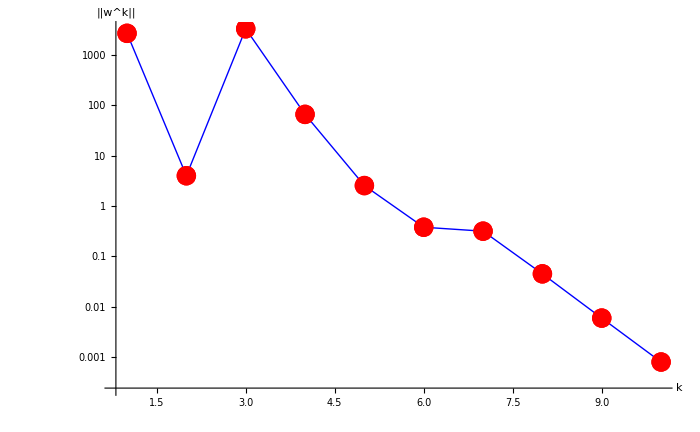

k | (X^k) | f(X^k) | ||w^k|| | κ
0 | ( -1.000, -2.000 ) | 1804. | 2687. | 1.
1 | ( -0.998, 0.997 ) | 3.993 | 3.999 | 0.98
2 | ( 0.958, -2.909 ) | 2928.745 | 3307.765 | 0.98
3 | ( 0.958, 0.841 ) | 1.173 | 66.084 | 0.96
4 | ( 0.959, 0.917 ) | 0.004 | 2.552 | 0.941
5 | ( 0.977, 0.953 ) | 0.0006 | 0.38 | 0.922
6 | ( 0.995, 0.989 ) | 0. | 0.317 | 0.904
7 | ( 0.999, 0.998 ) | 0. | 0.045 | 0.886
8 | ( 1.00, 1.00 ) | 0. | 0.006 | 0.868
9 | ( 1.00, 1.00 ) | 0. | 0.0008 | 0.851

```mathematica
PlotMethod[func,setX,setY,Res[[;;-3]]]
PlotNorms[norms]
MakeTable[Res]
```